```mathematica
exactSol[t_]=u[t]/.DSolve[{u'[t]==10u[t](1-u[t]),u[0]==0.1},u[t],t][[1]];
t0=0; T=1;
eplicitEuler[n_]:=(
h=N[(T-t0)/n];
y=Table[{0,0},n+1];
y[[1]]={t0,1};
For[i=1,i<Length[y],i++,
y[[i+1]]={t0 +i*h,y[[i,2]]-5*h *(y[[i,2]](1-y[[i,2]])+y[[i+1,2]](1-y[[i+1,2]]))};
];y)
```

```mathematica
ⅇ^(-10 t)
```

```mathematica
(*approxSolutions = {explicitEuler[4], explicitEuler[20],explicitEuler[100]};*)
```

```mathematica
(*RK3[f_,h_,t0_,T_,u0_]:=(n=Ceiling[(T-t0)/h]
y={u0}
t={t0}
t={t,t+h}
k1=hf[t
y={y,1/4k1 +3/4k3}
*)
```

```mathematica
(*f[t_,u_]:=-10u
explicitRK[f_,n_,t0_,T_,u0_]:=(
h=N[(T-t0)/n];
y=Table[{0,0},n+1];
y[[1]]={t0,u0};
For[i=1,i<Length[y],i++,
k1=h*f[y[[i,1]],y[[i,2]]];
k2=h*f[y[[i,1]]+1/3*h,y[[i,2]]+k1/3];
k3=h*f[y[[i,1]]+2/3*h,y[[i,2]]+2/3*k2];
y[[i+1,1]]= y[[i,1]]+h;
y[[i+1,2]]= y[[i,2]]+1/4*k1+3/4*k3;
];
y
)
(*ListPlot[explicitRK[f,10,0,6,1]]*)
Print[explicitRK[f,100,0,6,1]]*)
```

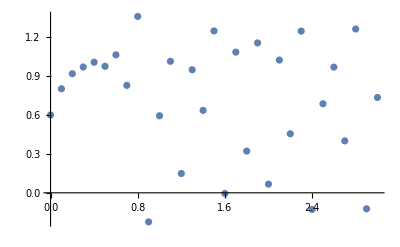

{{0,0.6},{0.1,0.802457},{0.2,0.918437},{0.3,0.970057},{0.4,1.00685},{0.5,0.975677},{0.6,1.06371},{0.7,0.828536},{0.8,1.35987},{0.9,-0.224246},{1.,0.59411},{1.1,1.01388},{1.2,0.149094},{1.3,0.949145},{1.4,0.635754},{1.5,1.24864},{1.6,-0.00526975},{1.7,1.08471},{1.8,0.321701},{1.9,1.1559},{2.,0.066834},{2.1,1.02362},{2.2,0.455247},{2.3,1.24674},{2.4,-0.128557},{2.5,0.686602},{2.6,0.969131},{2.7,0.400394},{2.8,1.26317},{2.9,-0.123418},{3.,0.734976}}

```mathematica
f[t_,u_]:=10 u*(1-u);
AB4[f_,h_,t0_,T_,u0_]:=(n=Ceiling[(T-t0)/h];y=Table[{0,0},n+1];
y[[1]]={t0,u0};
For[i=1,i<4,i++,k1=h*f[y[[i,1]],y[[i,2]]];
k2=h*f[y[[i,1]]+1/3*h,y[[i,2]]+k1/3];
k3=h*f[y[[i,1]]+2/3*h,y[[i,2]]+2/3*k2];
y[[i+1,1]]=y[[i,1]]+h;
y[[i+1,2]]=y[[i,2]]+1/4*k1+3/4*k3;];
For[i=4,i<Length[y],i++,y[[i+1,1]]=y[[i,1]]+h;
y[[i+1,2]]=y[[i,2]]+h/24*(55*f[y[[i,1]],y[[i,2]]]-59*f[y[[i-1,1]],y[[i-1,2]]]+37*f[y[[i-2,1]],y[[i-2,2]]]-9*f[y[[i-3,1]],y[[i-3,2]]])];
y);
ListPlot[AB4[f,.1,0,3,.6]]
Print[AB4[f,.1,0,3,.6]]
```